## Fibonacci Numbers Visibility

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
fib=Table[Fibonacci[x],{x,10000}];
```

## SDL Complexity

```mathematica
<<sdl.mx
```

```mathematica
sdl[fib]
```

{0.0000167764,0.999996}

## Visibility

```mathematica
<<visibility.mx
```

```mathematica
links=naturalVisibilityLinks[fib[[;;1000]]]
```

{1→2,1→7,1→8,1→9,1→10,1→11,1→12,1→13,1→14,1→15,1→16,1→17,1→18,1→19,1→20,1→21,1→22,1→23,1→24,1→25,1→26,1→27,1→28,1→29,1→30,1→31,1→32,1→33,1→34,1→35,1→36,1→37,498432,991→996,991→997,991→998,991→999,992→993,992→994,992→995,992→996,992→997,992→998,992→999,993→994,993→995,993→996,993→997,993→998,993→999,994→995,994→996,994→997,994→998,994→999,995→996,995→997,995→998,995→999,996→997,996→998,996→999,997→998,997→999,998→999}
 |  |  |  |

```mathematica
natGraph=Graph[links, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|994→1,998→994,996→2,997→2|>

```mathematica
natGraph
```

-Graphics-

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

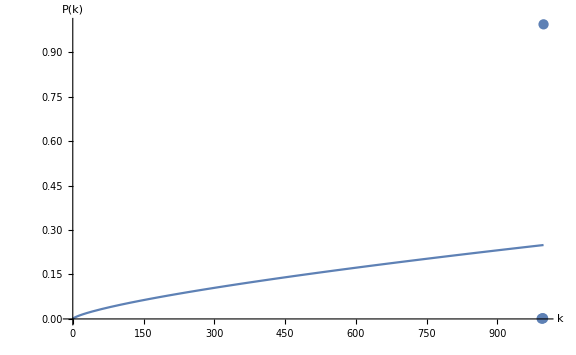
{{C→0.00171521,γ→-0.721039},-Graphics-}

```mathematica
plotModel[count,1000]
```

## Horizontal Visibility

```mathematica
horlinks=horizontalVisibilityLinks[fib[[;;10]]];
```

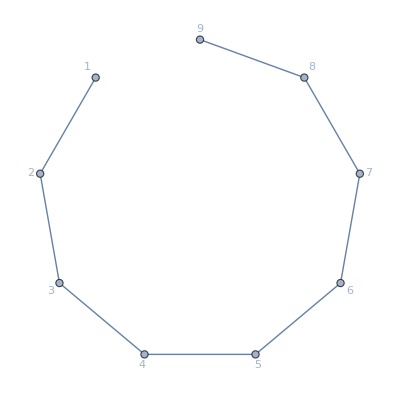

```mathematica
hg=Graph[horlinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding", VertexLabels->"Name"]
```

```mathematica
count=VertexDegree[hg]//Counts
```

<|1→2,2→997|>

```mathematica
natGraph
```

```mathematica
plotModel[count,1000]
```

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|994→1,998→994,996→2,997→2|>

```mathematica
natGraph
```

```mathematica
plotModel[count,1000]
```